## setup

### overhead

```mathematica
(* clear all variable names and assignments *)
Clear["Global`*"];ClearAll["Global`*"];Remove["Global`*"];ClearSystemCache[];
```

```mathematica
(* directory of Mathematica files *)
dirMathematica=Environment["HOME"]<>"/Mathematica_files/";

(* ln-fhs "/Users/dantopa/Dropbox/_mm" "/Users/dantopa/Mathematica_files" *)
(* packages shared by all notebooks *)
dirnb=dirMathematica<>"nb/";
dirPack=dirnb<>"packages/";

(* seed file *)
nbSeed="seed 19_12.nb";
```

### tag

```mathematica
home="ert/mercury/snake/";  
Get["utility modules.m",Path->dirPack];
stamp1;
```

CreateDirectory::filex: /Users/dantopa/Mathematica_files/io/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/mercury/ already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

maximum memory: 0.145848 GB

seed file: /Users/dantopa/Mathematica_files/nb/seed 19_12.nb

user: dantopa, CPU: Xiuhcoatl,  MM v. 12.0.0 for Mac OS X x86

date: Apr 27, 2020, time: 10:37:01

nb: /Users/dantopa/Mathematica_files/nb/ert/mercury/snake/fourier-cosine-02.nb

### modules, functions, settings, ...

#### admin

```mathematica
printmem
```

maximum memory: 0.145848 GB

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```

#### settings

```mathematica
exportFlag=True;
```

```mathematica
o={0,0};
```

```mathematica
guc=Circle[o,1];
```

```mathematica
ipad=ImagePadding->{{Automatic,3},{Automatic,Automatic}};
```

```mathematica
isize=ImageSize->5 72;
```

#### functions

#### substitutions

#### modules

## import

```mathematica
fullName=dirData<>"rcs-values.dat";
```

```mathematica
fullName=dirData<>"mean-total-rcs.dat";
```

```mathematica
meanRCS=Import[fullName];
```

```mathematica
mx=Max[meanRCS]
mn=Min[meanRCS]
```

117.022

20.7344

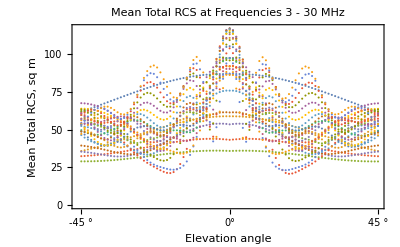

```mathematica
ListPlot[meanRCS,
ipad,
Frame->True,
FrameTicks->{{Automatic,Automatic},{{{1,-45°},{46,"0°"},{91,45°}},Automatic}},
FrameLabel->{"Elevation angle","Mean Total RCS, sq m"},
Frame->True,
PlotLabel->"Mean Total RCS at Frequencies 3 - 30 MHz"]
```

```mathematica
Dimensions[meanRCSᵀ]
```

{91,28}

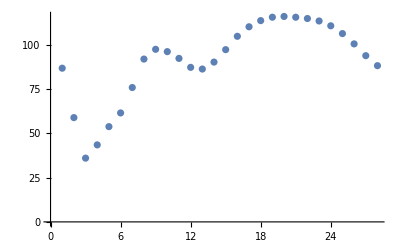

```mathematica
ListPlot[meanRCSᵀ[[45]]]
```

## loop

### pose problem

```mathematica
d=7;
basis=Table[Cos[k θ],{k,0,d}];
𝒩=d+1;
```

### prep

```mathematica
ν=Range[3,30];
```

```mathematica
μ=(2/27 #-11/9)&/@ν;
m=Length[μ]
```

28

```mathematica
one=Table[1,{m}];
A={one};
vector=1;
Do[
vector=vector μ;
AppendTo[A,vector]
,{k,d}];
A=Aᵀ;
W=A†.A;
Winv=Inverse[W];
det=Det[W]//N
```

0.000369424

```mathematica
s=SingularValueList[A];
κ=First[s]/Last[s]//N
```

214.949

```mathematica
Det[W]//N
```

0.000369424

### loop

```mathematica
file=dirData<>"fourier-d-"<>pad[d]<>".txt";
rslt=OpenWrite[file,PageWidth->Infinity];
(* tag source file *)
mark;
Write[rslt,dirHome,nb];
Write[rslt,time," ",date];
Write[rslt,""];
(* mesh *)
Write[rslt,"degree of fit: ",d];
Write[rslt,"mesh:"];
Write[rslt,μ];
Write[rslt,μ//N];
Write[rslt,"dimensions A = ",Dimensions[A]];
Write[rslt,"kappa(A) = ",κ];
Write[rslt,"det W: ",det];
Write[rslt,"Diagonal[Winv]: ",Diagonal[Winv]//N];
Write[rslt,""];
(* init *)
mxerr=-∞;
mnerr=∞;
smerr=0;
cnterr=0;
myerr={};
(* loop *)
Do[
b=S[[k]];
Write[rslt,""];
α=k-180-1;
Write[rslt,"k = ",k,"; alpha = ",α];
Write[rslt,"data vector:"];
Write[rslt,b];
(* solution *)
c=LeastSquares[A,b];
r=A.c-b;
te=r.r;
smerr=smerr+te;
cnterr++;
If[te>mxerr,mxerr=te;kmax=k;];
If[te<mnerr,mnerr=te;kmin=k];
myerr=AppendTo[myerr,{α,te}];
g[𝓍_]=c.basis;
𝓈=√((r.r)/(m-𝒩)Diagonal[Winv]);
sn=Abs[c]/𝓈;
counter=0;
(If[#<1,counter++])&/@sn;
(* output *)
Write[rslt,"Mean = ",FortranForm[Mean[b]]];
Write[rslt,"solution vector:"];
Write[rslt,c];
Write[rslt,"solution errors:"];
Write[rslt,𝓈];
Write[rslt,"solution function:"];
Write[rslt,g[x]];
Write[rslt,"residual error vector:"];
Write[rslt,r];
Write[rslt,"Sum of residuals = ",FortranForm[Total[r]]];
Write[rslt,"Standard deviation of residuals = ",FortranForm[StandardDeviation[r]]];
Write[rslt,"r^2 = ",te];
Write[rslt,"amplitude signal-to-noise:"];
Write[rslt,sn];
Write[rslt,"number where signal/noise < 1: ",counter, " of ",d+1," (",Round[1000 counter/(d+1)]/10//N,"%)"];
Write[rslt,"Mean value of data vector = ",Mean[b]];
,{k,360}];
Write[rslt,""];
Write[rslt,"Mean error = ",smerr/cnterr];
Write[rslt,"Maximum total error of ",mxerr," at k = ",kmax," (",kmax-181," deg)"];
Write[rslt,"Minimum total error of ",mnerr," at k = ",kmin," (",kmin-181," deg)"];
Write[rslt,""];
Write[rslt,""];
Close[rslt];
edit[file]
```

Removing quotes from /Users/dantopa/Mathematica_files/io/ert/mercury/snake/data/monomial-d-07.txt

```mathematica
file=dirData<>"error-log-"<>pad[d]<>".txt";
rslt=OpenWrite[file,PageWidth->Infinity];
(* tag source file *)
mark;
Write[rslt,dirHome,nb];
Write[rslt,time," ",date];
Write[rslt,""];
(* mesh *)
Write[rslt,"Spectrum of total error:"];
Write[rslt,myerr];
Close[rslt];
edit[file]
```

Removing quotes from /Users/dantopa/Mathematica_files/io/ert/mercury/snake/data/error-log-07.txt

## summary

```mathematica
gworst=ListPlot[{myerr[[181]]},PlotStyle->{Red,PointSize[0.02]}];
gbest=ListPlot[{myerr[[282]]},PlotStyle->{Green,PointSize[0.02]}];
```

```mathematica
g101=ListPlot[myerr,
ipad,
isize,
Frame->True,
FrameLabel->{"Yaw angle, °","Total Squared Error"},
PlotStyle->Black,
PlotLabel->"Sciacca Airframe"<>lf<>"Total Squared Error vs. Yaw Angle"];
```

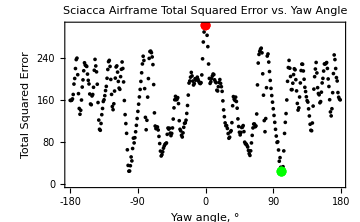

```mathematica
g102=Show[{g101,gbest,gworst},
ipad,
FrameTicks->{{Automatic,Automatic},{Range[-180,180,45],Automatic}}]
```

```mathematica
Export[dirData<>"scatter-error.pdf",g102]
```

/Users/dantopa/Mathematica_files/io/ert/mercury/snake/data/scatter-error.pdf

## end

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```